```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fplot[n_]:=DiscretePlot[PDF[BinomialDistribution[n,0.5],x],{x,0,n},PlotRange->{{-0.2,n+0.2},Full},Frame->{True,True,False,False},Axes->False,PlotMarkers->{Automatic, 9},PlotStyle->Blue,FrameTicks->{{0,{n,1}},None},FrameLabel->{"Fraction of heads","Probability"},LabelStyle->{Black,FontSize->18}]
```

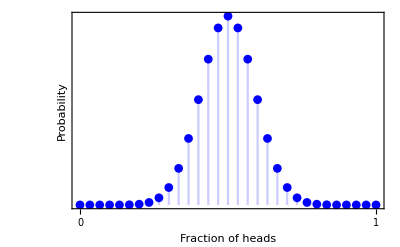

```mathematica
fplot[30]
```

```mathematica
g = fplot[1];
Export["../figures/binomial_1.pdf",g]
```

../figures/binomial_1.pdf

```mathematica
g = fplot[2];
Export["../figures/binomial_2.pdf",g]
```

../figures/binomial_2.pdf

```mathematica
g = fplot[5];
Export["../figures/binomial_5.pdf",g]
```

../figures/binomial_5.pdf

```mathematica
g = fplot[30];
Export["../figures/binomial_30.pdf",g]
```

../figures/binomial_30.pdf